```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub0/buffer/fpi.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub50/buffer/fpi.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub50/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub50=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub50=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub50linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub100/buffer/fpi.dat"]];
T100=Flatten[Import["./LPA_Tscaling_mub100/buffer/TMeV.dat"]];
t=(T100-T100[[1]])/T100[[1]];
datamub100=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub100=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];
b1mub100linear=Transpose[{T100[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub150/buffer/fpi.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub150/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub150=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub150=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub150linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub200/buffer/fpi.dat"]];
T200=Flatten[Import["./LPA_Tscaling_mub200/buffer/TMeV.dat"]];
t=(T200-T200[[1]])/T200[[1]];
datamub200=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub200=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];
b1mub200linear=Transpose[{T200[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub250/buffer/fpi.dat"]];
T250=Flatten[Import["./LPA_Tscaling_mub250/buffer/TMeV.dat"]];
t=(T250-T250[[1]])/T250[[1]];
datamub250=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub250=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T250]-2}]]}];
b1mub250linear=Transpose[{T250[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T250]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub300/buffer/fpi.dat"]];
T300=Flatten[Import["./LPA_Tscaling_mub300/buffer/TMeV.dat"]];
t=(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub350/buffer/fpi.dat"]];
T350=Flatten[Import["./LPA_Tscaling_mub350/buffer/TMeV.dat"]];
t=(T350-T350[[1]])/T350[[1]];
datamub350=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub350=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T350]-2}]]}];
b1mub350linear=Transpose[{T350[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T350]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub400/buffer/fpi.dat"]];
T400=Flatten[Import["./LPA_Tscaling_mub400/buffer/TMeV.dat"]];
t=(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub450/buffer/fpi.dat"]];
T450=Flatten[Import["./LPA_Tscaling_mub450/buffer/TMeV.dat"]];
t=(T450-T450[[1]])/T450[[1]];
datamub450=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub450=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];
b1mub450linear=Transpose[{T450[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub500/buffer/fpi.dat"]];
T500=Flatten[Import["./LPA_Tscaling_mub500/buffer/TMeV.dat"]];
t=(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub550/buffer/fpi.dat"]];
T550=Flatten[Import["./LPA_Tscaling_mub550/buffer/TMeV.dat"]];
t=(T550-T550[[1]])/T550[[1]];
datamub550=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub550=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];
b1mub550linear=Transpose[{T550[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub575/buffer/fpi.dat"]];
T575=Flatten[Import["./LPA_Tscaling_mub575/buffer/TMeV.dat"]];
t=(T575-T575[[1]])/T575[[1]];
datamub575=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub575=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];
b1mub575linear=Transpose[{T575[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub600/buffer/fpi.dat"]];
T600=Flatten[Import["./LPA_Tscaling_mub600/buffer/TMeV.dat"]];
t=(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
b1mub600linear=Transpose[{T600[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub625/buffer/fpi.dat"]];
T625=Flatten[Import["./LPA_Tscaling_mub625/buffer/TMeV.dat"]];
t=(T625-T625[[1]])/T625[[1]];
datamub625=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub625=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub625[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T625]-2}]]}];
b1mub625linear=Transpose[{T625[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub625[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T625]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub650/buffer/fpi.dat"]];
T650=Flatten[Import["./LPA_Tscaling_mub650/buffer/TMeV.dat"]];
t=(T650-T650[[1]])/T650[[1]];
datamub650=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub650=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T650]-2}]]}];
b1mub650linear=Transpose[{T650[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T650]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub675/buffer/fpi.dat"]];
T675=Flatten[Import["./LPA_Tscaling_mub675/buffer/TMeV.dat"]];
t=(T675-T675[[1]])/T675[[1]];
datamub675=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub675=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub675[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T675]-2}]]}];
b1mub675linear=Transpose[{T675[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub675[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T675]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub700/buffer/fpi.dat"]];
T700=Flatten[Import["./LPA_Tscaling_mub700/buffer/TMeV.dat"]];
t=(T700-T700[[1]])/T700[[1]];
datamub700=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
b1mub700linear=Transpose[{T700[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub705/buffer/fpi.dat"]];
T703=Flatten[Import["./LPA_Tscaling_mub705/buffer/TMeV.dat"]];
t=(T703-T703[[1]])/T703[[1]];
datamub703=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub703=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub703[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T703]-2}]]}];
b1mub703linear=Transpose[{T703[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub703[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T703]-2}]]}];
```

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub0/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub0/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub50/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub50/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub100/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub100/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub150/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub150/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub200/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub200/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub250/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub250/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub300/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub300/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub350/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub350/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub400/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub400/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub450/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub450/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub500/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub500/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub550/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub550/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub575/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub575/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub600/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub600/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub625/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub625/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub650/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub650/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub675/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub675/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub700/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub700/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub705/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_Tscaling_mub705/buffer/TMeV.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 2.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 2 至 0.

Transpose::nmtx: {Flatten[$Failed]⟦2;;0⟧,{}} 的前两层无法转置.

## Plot

Part::take: 无法在 (-1. $Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

Transpose::nmtx: {Log[-1. (-1. $Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 (-1. $Failed+Flatten[$Failed])/($Failed) 中提取位置 2 至 0.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

Transpose::nmtx: {Log[-1. (-1. $Failed+Flatten[$Failed])/($Failed)⟦2;;0⟧],{}} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

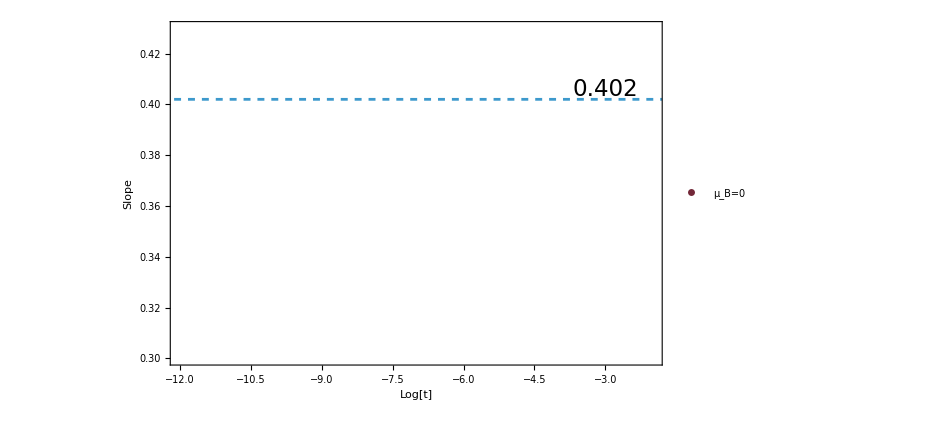

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub50,b1mub100,b1mub150,b1mub200,b1mub250,b1mub300,b1mub350,b1mub400,b1mub450,b1mub500,b1mub550(*,b1mub575*),b1mub600(*,b1mub625*),b1mub650(*,b1mub675*),b1mub700,b1mub703},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["Slope",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.05}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.3,0.43}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.402},{10,0.402}},PlotStyle->Dashed],ImageSize->700,Background->None,Epilog->{Text[Style["0.402",23],{-3,0.406}]}]
```

```mathematica
Export["./Tscaling.pdf",plotT]
```

./Tscaling.pdf

```mathematica
muball=Table[i,{i,0,700,50}];
dataall={b1mub0,b1mub50,b1mub100,b1mub150,b1mub200,b1mub250,b1mub300,b1mub350,b1mub400,b1mub450,b1mub500,b1mub550,b1mub575,b1mub600,b1mub625,b1mub650,b1mub675,b1mub700};
lineardataall={b1mub0linear,b1mub50linear,b1mub100linear,b1mub150linear,b1mub200linear,b1mub250linear,b1mub300linear,b1mub350linear,b1mub400linear,b1mub450linear,b1mub500linear,b1mub550linear,b1mub575linear,b1mub600linear,b1mub625linear,b1mub650linear,b1mub675linear,b1mub700linear};
```

```mathematica
(*Export["Tscaling.pdf",plotT];*)
```

```mathematica
Table[Export["./T_scaling_data/mub"<>ToString[muball[[i]]]<>".dat",dataall[[i]]],{i,1,Length[muball]}]
```

{./T_scaling_data/mub0.dat,./T_scaling_data/mub50.dat,./T_scaling_data/mub100.dat,./T_scaling_data/mub150.dat,./T_scaling_data/mub200.dat,./T_scaling_data/mub250.dat,./T_scaling_data/mub300.dat,./T_scaling_data/mub350.dat,./T_scaling_data/mub400.dat,./T_scaling_data/mub450.dat,./T_scaling_data/mub500.dat,./T_scaling_data/mub550.dat,./T_scaling_data/mub600.dat,./T_scaling_data/mub650.dat,./T_scaling_data/mub700.dat}

```mathematica
muball2={0,50,100,150,200,250,300,350,400,450,500,550,575,600,625,650,675,700};
Table[Export["./T_scaling_data_hot/mub"<>ToString[muball2[[i]]]<>".dat",lineardataall[[i]]],{i,1,Length[muball2]}]
```

{./T_scaling_data_hot/mub0.dat,./T_scaling_data_hot/mub50.dat,./T_scaling_data_hot/mub100.dat,./T_scaling_data_hot/mub150.dat,./T_scaling_data_hot/mub200.dat,./T_scaling_data_hot/mub250.dat,./T_scaling_data_hot/mub300.dat,./T_scaling_data_hot/mub350.dat,./T_scaling_data_hot/mub400.dat,./T_scaling_data_hot/mub450.dat,./T_scaling_data_hot/mub500.dat,./T_scaling_data_hot/mub550.dat,./T_scaling_data_hot/mub575.dat,./T_scaling_data_hot/mub600.dat,./T_scaling_data_hot/mub625.dat,./T_scaling_data_hot/mub650.dat,./T_scaling_data_hot/mub675.dat,./T_scaling_data_hot/mub700.dat}

# μ_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_muscaling_frommub100/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub100/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub100=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub100=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub100linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub200/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub200/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub200=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub200=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub200linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub300/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub300/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub300=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub300=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub300linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub400/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub400/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub400=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub400=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub400linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub500/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub500/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub500=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub500=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub500linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub600/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub600/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub600=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub600=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub600linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub650/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub650/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub650=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub650=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub650linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
fpi=Flatten[Import["./LPA_muscaling_frommub700/buffer/fpi.dat"]];
mub=Flatten[Import["./LPA_muscaling_frommub700/buffer/mub.dat"]];
mub1=(mub-mub[[1]])/mub[[1]];
mudatamub700=Transpose[{Log[-mub1],Log[fpi]}];
mub1mub700=Transpose[{Log[-mub1[[3;;Length[mub1]-2]]],Flatten[Table[FindFit[mudatamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
mub700linear=Transpose[{mub[[3;;Length[mub]-2]],Flatten[Table[FindFit[mudatamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,3,Length[mub1]-2}]]}];
```

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub100/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub100/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub200/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub200/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub300/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub300/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub400/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub400/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub500/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub500/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub600/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub600/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub650/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub650/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub700/buffer/fpi.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./LPA_muscaling_frommub700/buffer/mub.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Part::take: 无法在 (-$Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-(-$Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 Flatten[$Failed] 中提取位置 3 至 -1.

Transpose::nmtx: {Flatten[$Failed]⟦3;;-1⟧,{}} 的前两层无法转置.

## Plot

```mathematica
plotmu=Show[ListLinePlot[{{-12,0.399},{1,0.399}}],ListPlot[{mub1mub100,mub1mub200,mub1mub300,mub1mub400,mub1mub500,mub1mub600,mub1mub650,mub1mub700},PlotLegends->{"μ_B=100MeV","μ_B=200MeV","μ_B=300MeV","μ_B=400MeV","μ_B=500MeV","μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"},AxesLabel->{"Log[μ]","β_μ"}],PlotRange->{{-12,-2},{0.3,0.5}}]
```

Part::take: 无法在 (-1. $Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

Transpose::nmtx: {Log[-1. (-1. $Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

Part::take: 无法在 (-1. $Failed+Flatten[$Failed])/($Failed) 中提取位置 3 至 0.

General::stop: 在本次计算中，Part::take 的进一步输出将被抑制.

Transpose::nmtx: {Log[-1. (-1. $Failed+Flatten[$Failed])/($Failed)⟦3;;0⟧],{}} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

-Graphics-

```mathematica
(*Export["muscaling.pdf",plotmu]*)
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["./pionmass/LPA_hscaling_mub0/buffer/mPion.dat"]];
```

```mathematica
fpi=Flatten[Import["./LPA_hscaling_mub0/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub0=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub0linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub50/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub50/buffer/c.dat"]]*197.33^3;
datamub50=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub50=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub50linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub100/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub100/buffer/c.dat"]]*197.33^3;
datamub100=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub100=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub100linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub150/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub150/buffer/c.dat"]]*197.33^3;
datamub150=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub150=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub150linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub200/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub200/buffer/c.dat"]]*197.33^3;
datamub200=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub200=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub200linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub250/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub250/buffer/c.dat"]]*197.33^3;
datamub250=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub250=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub250linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub300/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub300=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub300linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub350/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub350/buffer/c.dat"]]*197.33^3;
datamub350=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub350=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub350linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub400/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub400=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub400linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub450/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub450/buffer/c.dat"]]*197.33^3;
datamub450=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub450=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub450linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub500/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub500=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub500linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub550/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub550/buffer/c.dat"]]*197.33^3;
datamub550=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub550=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub550linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub600/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub600/buffer/c.dat"]]*197.33^3;
datamub600=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub600=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub600linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub650/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub650/buffer/c.dat"]]*197.33^3;
datamub650=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub650=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub650linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPA_hscaling_mub700/buffer/fpi.dat"]];
h=Flatten[Import["./LPA_hscaling_mub700/buffer/c.dat"]]*197.33^3;
datamub700=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub700=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub700linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
```

## Plot

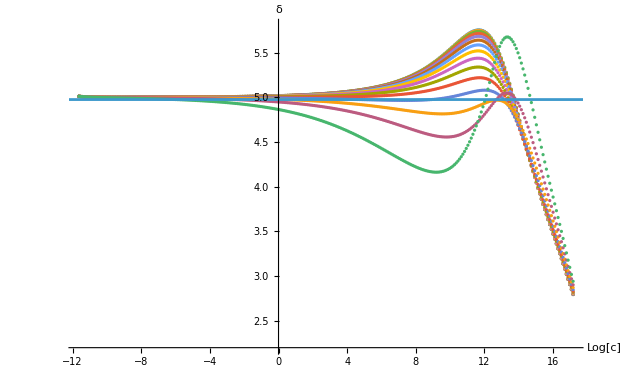

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub50,h1mub100,h1mub150,h1mub200,h1mub250,h1mub300,h1mub350,h1mub400,h1mub450,h1mub500,h1mub550,h1mub600,h1mub650,h1mub700},AxesLabel->{"Log[c]","δ"},PlotLegends->{(*"μ_B=0","μ_B=50MeV","μ_B=100MeV","μ_B=150MeV","μ_B=200MeV","μ_B=250MeV","μ_B=300MeV","μ_B=350MeV",*)(*"μ_B=400MeV","μ_B=450MeV","μ_B=500MeV","μ_B=550MeV"*)(*,"μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"*)},Axes->True,PlotRange->{All,{2.2,5.8}}],ListLinePlot[{{-20,4.975},{100,4.975}}]]
```

```mathematica
Export["./LPA_Tscaling_hot/mub0.dat",h1mub0linear];
Export["./LPA_Tscaling_hot/mub50.dat",h1mub50linear];
Export["./LPA_Tscaling_hot/mub100.dat",h1mub100linear];
Export["./LPA_Tscaling_hot/mub150.dat",h1mub150linear];
Export["./LPA_Tscaling_hot/mub200.dat",h1mub200linear];
Export["./LPA_Tscaling_hot/mub250.dat",h1mub250linear];
Export["./LPA_Tscaling_hot/mub300.dat",h1mub300linear];
Export["./LPA_Tscaling_hot/mub350.dat",h1mub350linear];
Export["./LPA_Tscaling_hot/mub400.dat",h1mub400linear];
Export["./LPA_Tscaling_hot/mub450.dat",h1mub450linear];
Export["./LPA_Tscaling_hot/mub500.dat",h1mub500linear];
Export["./LPA_Tscaling_hot/mub550.dat",h1mub550linear];
Export["./LPA_Tscaling_hot/mub600.dat",h1mub600linear];
Export["./LPA_Tscaling_hot/mub650.dat",h1mub650linear];
Export["./LPA_Tscaling_hot/mub700.dat",h1mub700linear];
```

# plot on phase diagram

## data

```mathematica
mub0data=Table[{0,Transpose[b1mub0linear][[1]][[i]],Transpose[b1mub0linear][[2]][[i]]},{i,1,Length[b1mub0linear]}];
mub50data=Table[{50,Transpose[b1mub50linear][[1]][[i]],Transpose[b1mub50linear][[2]][[i]]},{i,1,Length[b1mub50linear]}];
mub100data=Table[{100,Transpose[b1mub100linear][[1]][[i]],Transpose[b1mub100linear][[2]][[i]]},{i,1,Length[b1mub100linear]}];
mub150data=Table[{150,Transpose[b1mub150linear][[1]][[i]],Transpose[b1mub150linear][[2]][[i]]},{i,1,Length[b1mub150linear]}];
mub200data=Table[{200,Transpose[b1mub200linear][[1]][[i]],Transpose[b1mub200linear][[2]][[i]]},{i,1,Length[b1mub200linear]}];
mub250data=Table[{250,Transpose[b1mub250linear][[1]][[i]],Transpose[b1mub250linear][[2]][[i]]},{i,1,Length[b1mub250linear]}];
mub300data=Table[{300,Transpose[b1mub300linear][[1]][[i]],Transpose[b1mub300linear][[2]][[i]]},{i,1,Length[b1mub300linear]}];
mub350data=Table[{350,Transpose[b1mub350linear][[1]][[i]],Transpose[b1mub350linear][[2]][[i]]},{i,1,Length[b1mub350linear]}];
mub400data=Table[{400,Transpose[b1mub400linear][[1]][[i]],Transpose[b1mub400linear][[2]][[i]]},{i,1,Length[b1mub400linear]}];
mub450data=Table[{450,Transpose[b1mub450linear][[1]][[i]],Transpose[b1mub450linear][[2]][[i]]},{i,1,Length[b1mub450linear]}];
mub500data=Table[{500,Transpose[b1mub500linear][[1]][[i]],Transpose[b1mub500linear][[2]][[i]]},{i,1,Length[b1mub500linear]}];
mub550data=Table[{550,Transpose[b1mub550linear][[1]][[i]],Transpose[b1mub550linear][[2]][[i]]},{i,1,Length[b1mub550linear]}];
mub575data=Table[{575,Transpose[b1mub575linear][[1]][[i]],Transpose[b1mub575linear][[2]][[i]]},{i,1,Length[b1mub575linear]}];
mub600data=Table[{600,Transpose[b1mub600linear][[1]][[i]],Transpose[b1mub600linear][[2]][[i]]},{i,1,Length[b1mub600linear]}];
mub625data=Table[{625,Transpose[b1mub625linear][[1]][[i]],Transpose[b1mub625linear][[2]][[i]]},{i,1,Length[b1mub625linear]}];
mub650data=Table[{650,Transpose[b1mub650linear][[1]][[i]],Transpose[b1mub650linear][[2]][[i]]},{i,1,Length[b1mub650linear]}];
mub675data=Table[{675,Transpose[b1mub675linear][[1]][[i]],Transpose[b1mub675linear][[2]][[i]]},{i,1,Length[b1mub675linear]}];
mub700data=Table[{700,Transpose[b1mub700linear][[1]][[i]],Transpose[b1mub700linear][[2]][[i]]},{i,1,Length[b1mub700linear]}];
```

Part::partw: ( 的部分 2 不存在.

```mathematica
mumub100data=Table[{Transpose[mub100linear][[1]][[i]],131.1413090,Transpose[mub100linear][[2]][[i]]},{i,1,Length[mub100linear]}];
mumub200data=Table[{Transpose[mub200linear][[1]][[i]],128.063591,Transpose[mub200linear][[2]][[i]]},{i,1,Length[mub200linear]}];
mumub300data=Table[{Transpose[mub300linear][[1]][[i]],122.759313,Transpose[mub300linear][[2]][[i]]},{i,1,Length[mub300linear]}];
mumub400data=Table[{Transpose[mub400linear][[1]][[i]],114.915769,Transpose[mub400linear][[2]][[i]]},{i,1,Length[mub400linear]}];
mumub500data=Table[{Transpose[mub500linear][[1]][[i]],103.947155,Transpose[mub500linear][[2]][[i]]},{i,1,Length[mub500linear]}];
mumub600data=Table[{Transpose[mub600linear][[1]][[i]],88.6153476,Transpose[mub600linear][[2]][[i]]},{i,1,Length[mub600linear]}];
mumub650data=Table[{Transpose[mub650linear][[1]][[i]],78.395755,Transpose[mub650linear][[2]][[i]]},{i,1,Length[mub650linear]}];
mumub700data=Table[{Transpose[mub700linear][[1]][[i]],64.8265550,Transpose[mub700linear][[2]][[i]]},{i,1,Length[mub700linear]}];
```

Part::partw: ( 的部分 2 不存在.

## Plot

```mathematica
(*ListContourPlot[Flatten[{mumub100data,mumub200data,mumub300data,mumub400data,mumub500data,mumub600data,mumub650data,mumub700data},1],Contours->{0.35,0.36,0.37,0.38,0.39,0.4}],*)
plot=ListContourPlot[Flatten[{mub0data,mub50data,mub100data,mub150data,mub200data,mub250data,mub300data,mub350data,mub400data,mub450data,mub500data,mub550data,mub575data,mub600data,mub625data,mub650data,mub675data,mub700data},1],Contours->{0.34,0.35,0.36,0.37,0.38,0.39,0.4},PlotRange->{{0,800},{50,135}}]
```

ListContourPlot::arrayerr: {{0,{Flatten[$Failed]⟦2;;0⟧,{}},(},{50.,{Flatten[$Failed]⟦2;;0⟧,{}},(},«14»,{675.,{Flatten[$Failed]⟦2;;0⟧,{}},(},{700.,{Flatten[$Failed]⟦2;;0⟧,{}},(}} 必须是一个有效数组.

ListContourPlot[{{0,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{50,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{100,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{150,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{200,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{250,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{300,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{350,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{400,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{450,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{500,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{550,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{575,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{600,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{625,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{650,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{675,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]},{700,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[(Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}])]}},Contours→{0.34,0.35,0.36,0.37,0.38,0.39,0.4},PlotRange→{{0,800},{50,135}}]

## 2D data

```mathematica
(*mub0datafit=Interpolation[Transpose[{Transpose[mub0data][[2]],Transpose[mub0data][[3]]}],InterpolationOrder->1];
mub50datafit=Interpolation[Transpose[{Transpose[mub50data][[2]],Transpose[mub50data][[3]]}],InterpolationOrder->1];
mub100datafit=Interpolation[Transpose[{Transpose[mub100data][[2]],Transpose[mub100data][[3]]}],InterpolationOrder->1];
mub150datafit=Interpolation[Transpose[{Transpose[mub150data][[2]],Transpose[mub150data][[3]]}],InterpolationOrder->1];
mub200datafit=Interpolation[Transpose[{Transpose[mub200data][[2]],Transpose[mub200data][[3]]}],InterpolationOrder->1];
mub250datafit=Interpolation[Transpose[{Transpose[mub250data][[2]],Transpose[mub250data][[3]]}],InterpolationOrder->1];
mub300datafit=Interpolation[Transpose[{Transpose[mub300data][[2]],Transpose[mub300data][[3]]}],InterpolationOrder->1];
mub350datafit=Interpolation[Transpose[{Transpose[mub350data][[2]],Transpose[mub350data][[3]]}],InterpolationOrder->1];
mub400datafit=Interpolation[Transpose[{Transpose[mub400data][[2]],Transpose[mub400data][[3]]}],InterpolationOrder->1];
mub450datafit=Interpolation[Transpose[{Transpose[mub450data][[2]],Transpose[mub450data][[3]]}],InterpolationOrder->1];
mub500datafit=Interpolation[Transpose[{Transpose[mub500data][[2]],Transpose[mub500data][[3]]}],InterpolationOrder->1];
mub550datafit=Interpolation[Transpose[{Transpose[mub550data][[2]],Transpose[mub550data][[3]]}],InterpolationOrder->1];
mub575datafit=Interpolation[Transpose[{Transpose[mub575data][[2]],Transpose[mub575data][[3]]}],InterpolationOrder->1];
mub600datafit=Interpolation[Transpose[{Transpose[mub600data][[2]],Transpose[mub600data][[3]]}],InterpolationOrder->1];
mub625datafit=Interpolation[Transpose[{Transpose[mub625data][[2]],Transpose[mub625data][[3]]}],InterpolationOrder->1];
mub650datafit=Interpolation[Transpose[{Transpose[mub650data][[2]],Transpose[mub650data][[3]]}],InterpolationOrder->1];
mub675datafit=Interpolation[Transpose[{Transpose[mub675data][[2]],Transpose[mub675data][[3]]}],InterpolationOrder->1];
mub700datafit=Interpolation[Transpose[{Transpose[mub700data][[2]],Transpose[mub700data][[3]]}],InterpolationOrder->1];*)
```

```mathematica
(*stepsize=0.01;
data2D={Table[If[x>Transpose[mub0data][[2]][[-1]],mub0datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub50data][[2]][[-1]]&&x<Transpose[mub50data][[2]][[1]],mub50datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub100data][[2]][[-1]]&&x<Transpose[mub100data][[2]][[1]],mub100datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub150data][[2]][[-1]]&&x<Transpose[mub150data][[2]][[1]],mub150datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub200data][[2]][[-1]]&&x<Transpose[mub200data][[2]][[1]],mub200datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub250data][[2]][[-1]]&&x<Transpose[mub250data][[2]][[1]],mub250datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub300data][[2]][[-1]]&&x<Transpose[mub300data][[2]][[1]],mub300datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub350data][[2]][[-1]]&&x<Transpose[mub350data][[2]][[1]],mub350datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub400data][[2]][[-1]]&&x<Transpose[mub400data][[2]][[1]],mub400datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub450data][[2]][[-1]]&&x<Transpose[mub450data][[2]][[1]],mub450datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub500data][[2]][[-1]]&&x<Transpose[mub500data][[2]][[1]],mub500datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub550data][[2]][[-1]]&&x<Transpose[mub550data][[2]][[1]],mub550datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub575data][[2]][[-1]]&&x<Transpose[mub575data][[2]][[1]],mub575datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub600data][[2]][[-1]]&&x<Transpose[mub600data][[2]][[1]],mub600datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub625data][[2]][[-1]]&&x<Transpose[mub625data][[2]][[1]],mub625datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub650data][[2]][[-1]]&&x<Transpose[mub650data][[2]][[1]],mub650datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub675data][[2]][[-1]]&&x<Transpose[mub675data][[2]][[1]],mub675datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub700data][[2]][[-1]]&&x<Transpose[mub700data][[2]][[1]],mub700datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}]};*)
```

```mathematica
(*Export["./T_scaling_data_hot/data2D.dat",data2D];*)
```

```mathematica
(*Export["./T_scaling_data_hot/T.dat",Table[i,{i,60,Transpose[mub0data][[2]][[1]],0.01}]];*)
```